```mathematica
Module[{data,res},
res=Map[CompoundExpression[
data=CellularAutomaton[
{#,3,1},{{1},0},56],
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,17Sqrt[Length[data]+1]}
],Style[50,"Text",Italic,Gray,11]]]&,
{926580123861,1296494317629,1727430646443,1751808437655,
4724926718037,3989490517413,5808233377692,4007712136038,6286883366814,6338043359340,7081173215451,4293674679165,
3027807734865,5496398003427}];
Style[res,LineSpacing->{1.2,0}]
]
```

```mathematica
Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 50&]
```

<|{1033434009042,134217727}→50,{1296494317629,134217727}→50,{1322812205502,134217727}→50,{144126485412,134217727}→50,{1727384411076,58654719}→50,{1727430646443,134217727}→50,{1751808437655,134217727}→50,{1818096668529,134217727}→50,{2185756612074,134217727}→50,{2456174919102,134217727}→50,{2896870376106,134217727}→50,{3027807734865,134217727}→50,{3296578258521,134217727}→50,{3351292530075,134217727}→50,{344120671410,125820927}→50,{3648564352275,134217727}→50,{3965869246785,134217727}→50,{3989490517413,134217727}→50,{4007712136038,134217727}→50,{4022743649019,134217727}→50,{4061460206493,134217727}→50,{4293674679165,134217727}→50,{437088661413,134217727}→50,{447552734298,134217727}→50,{4495982101881,134217727}→50,{4609897374417,134217727}→50,{4724926718037,134217727}→50,{499802006211,134217727}→50,{5311584073221,134217727}→50,{5398724993478,134217727}→50,{5423217456120,134217727}→50,{5496398003427,134217727}→50,{5541729979884,134217727}→50,{5558035947783,134217727}→50,{5560363423086,134217727}→50,{5607975695100,134217727}→50,{5618455595277,134217727}→50,{5808233377692,134217727}→50,{5992770446358,134217727}→50,{6013709814354,134217727}→50,{6091554933015,134217727}→50,{6286883366814,134217727}→50,{6297373478661,134217727}→50,{6338043359340,134217727}→50,{6940203681498,134217727}→50,{7081173215451,134217727}→50,{926580123861,134217727}→50|>

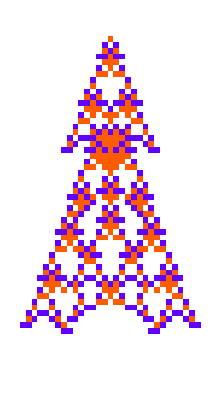
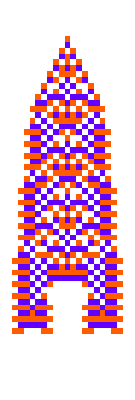
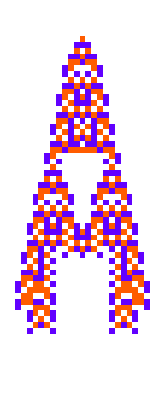
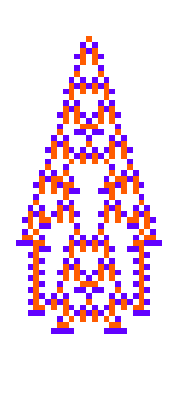
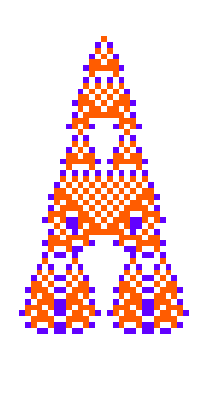
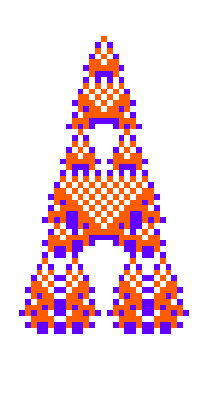
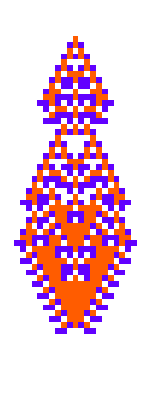
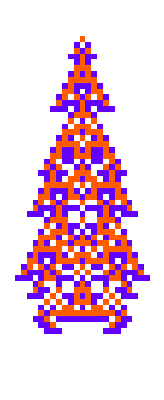

```mathematica
KeyValueMap[ArrayPlot[CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, 55], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 50&]]
```

```mathematica
Length[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 50&]]
```

47

```mathematica
Module[
{goal=50,deep=5000,cut=200,ru,life,data,res},
res=ParallelTable[
SeedRandom[745746+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#],5],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life!=-Infinity&&Abs[life-goal]<=
Abs[Last[#]-goal],{ru,life},#]
]&,{{0,4,1},0},deep],{i,{2}}];
]
```

```mathematica
ArrayPlot[CellularAutomaton[evo[[-1, 1]], {{1}, 0}, {55, {-20,20}}]]
```

-Graphics-

```mathematica
Module[{ca = CellularAutomaton[evo[[-1, 1]], {{1}, 0}, {55, {-20,20}}]},Select[Table[{{"[◼]", "RandomRuleMutation"}}[evo[[-1, 1]]], 1000], With[{nca =CellularAutomaton[#, {{1}, 0}, {55, {-20,20}}]}, nca=!= ca&&{{"[◼]", "TestCALifeTime"}}[nca]== 50]&]]
```

{}

```mathematica
{{"[◼]", "quickneutral"}}[evo[[-1, 1]]]
```

{{319777654365456165459980241633050129676,4,1},{319777654365456165459980241633318565132,4,1},{319777654365456165459980241633587000588,4,1},{319777654365456165459980241633855436044,4,1},{319777654365456166640571862350461433100,4,1},{319777654365456166640571862350729868556,4,1},{319777654365456166640571862350998304012,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456167821163483067872736524,4,1},{319777654365456167821163483068141171980,4,1},{319777654365456167821163483068409607436,4,1},{319777654365456167821163483068678042892,4,1},{319777654365456169001755103785284039948,4,1},{319777654365456169001755103785552475404,4,1},{319777654365456169001755103785820910860,4,1},{319777654365456169001755103786089346316,4,1},{319798423552890304770494363618367010060,4,1},{319798423552890304770494363618635445516,4,1},{319798423552890304770494363618903880972,4,1},{319798423552890304770494363619172316428,4,1},{319798423552890305951085984335778313484,4,1},{319798423552890305951085984336046748940,4,1},{319798423552890305951085984336315184396,4,1},{319798423552890305951085984336583619852,4,1},{319798423552890307131677605053189616908,4,1},{319798423552890307131677605053458052364,4,1},{319798423552890307131677605053726487820,4,1},{319798423552890307131677605053994923276,4,1},{319798423552890308312269225770600920332,4,1},{319798423552890308312269225770869355788,4,1},{319798423552890308312269225771137791244,4,1},{319798423552890308312269225771406226700,4,1},{319819192740324444081008485603683890444,4,1},{319819192740324444081008485603952325900,4,1},{319819192740324444081008485604220761356,4,1},{319819192740324444081008485604489196812,4,1},{319819192740324445261600106321095193868,4,1},{319819192740324445261600106321363629324,4,1},{319819192740324445261600106321632064780,4,1},{319819192740324445261600106321900500236,4,1},{319819192740324446442191727038506497292,4,1},{319819192740324446442191727038774932748,4,1},{319819192740324446442191727039043368204,4,1},{319819192740324446442191727039311803660,4,1},{319819192740324447622783347755917800716,4,1},{319819192740324447622783347756186236172,4,1},{319819192740324447622783347756454671628,4,1},{319819192740324447622783347756723107084,4,1},{319839961927758583391522607589000770828,4,1},{319839961927758583391522607589269206284,4,1},{319839961927758583391522607589537641740,4,1},{319839961927758583391522607589806077196,4,1},{319839961927758584572114228306412074252,4,1},{319839961927758584572114228306680509708,4,1},{319839961927758584572114228306948945164,4,1},{319839961927758584572114228307217380620,4,1},{319839961927758585752705849023823377676,4,1},{319839961927758585752705849024091813132,4,1},{319839961927758585752705849024360248588,4,1},{319839961927758585752705849024628684044,4,1},{319839961927758586933297469741234681100,4,1},{319839961927758586933297469741503116556,4,1},{319839961927758586933297469741771552012,4,1},{319839961927758586933297469742039987468,4,1}}

```mathematica
Length[]
```

64

```mathematica
NestGraph[{{"[◼]", "quickneutral"}}, {evo[[-1, 1]]}, 2]
```

-Graphics-

```mathematica
VertexCount[]
```

64

```mathematica
exhaustiveneutral[ru_, cut_:200]:= 
With[{lt = {{"[◼]", "TestLifetime"}}[ru, cut]}, Select[getallmutations[ru], {{"[◼]", "TestLifetime"}}[#, cut] == lt&]]
```

```mathematica
{{"[◼]", "TestLifetime"}}[evo[[-1, 1]], 55]
```

50

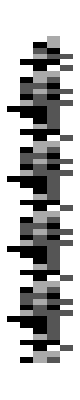
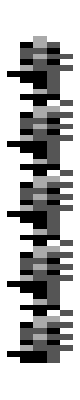
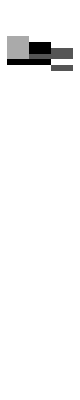
{-Graphics-36,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics--∞,-Graphics-19,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-29,-Graphics-51,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-33,-Graphics-32,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-29,-Graphics--∞,-Graphics--∞,-Graphics-26,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-29,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-51,-Graphics-41,-Graphics-34,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-18,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-26,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-9,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-29,-Graphics--∞,-Graphics-39,-Graphics-27,-Graphics-41,-Graphics--∞,-Graphics--∞,-Graphics-30,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-33,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics--∞,-Graphics-29,-Graphics--∞,-Graphics--∞,-Graphics-11,-Graphics--∞,-Graphics--∞,-Graphics-27,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-40,-Graphics-52,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-25,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics--∞,-Graphics-6,-Graphics--∞,-Graphics--∞}

```mathematica
With[{ca = CellularAutomaton[#, {{1}, 0}, 55]}, Labeled[ArrayPlot[ca],{{"[◼]", "TestCALifeTime"}}[ca]]]& /@ getallmutations[evo[[-1, 1]]]
```

```mathematica
exhaustiveneutral[#, 55]&[evo[[-1, 1]]]
```

{}

```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] := 
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
ClearAll@exhaustiveneutral
exhaustiveneutral[ru_, cut_:200]:= 
With[{lt = {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, cut]]}, Select[getallmutations[ru], {{"[◼]", "TestLifetime"}}[#, cut] == lt&]]
```

```mathematica
exhaustiveneutral[evo[[-1, 1]]]
```

{{319777654365456166640571862350729868556,4,1},{319798423552890305951085984336046748940,4,1},{319819192740324445261600106321363629324,4,1},{319839961927758583391522607589269206284,4,1},{319839961927758585752705849024091813132,4,1},{319839961927758586933297469741503116556,4,1},{319839961927758584572114228306412074252,4,1},{319839961927758584572114228306948945164,4,1},{319839961927758584572114228307217380620,4,1}}

```mathematica
Select[getallmutations[evo[[-1, 1]]], {{"[◼]", "TestLifetime"}}[#, 55] == 50&]
```

{{319777654365456166640571862350729868556,4,1},{319798423552890305951085984336046748940,4,1},{319819192740324445261600106321363629324,4,1},{319839961927758583391522607589269206284,4,1},{319839961927758585752705849024091813132,4,1},{319839961927758586933297469741503116556,4,1},{319839961927758584572114228306412074252,4,1},{319839961927758584572114228306948945164,4,1},{319839961927758584572114228307217380620,4,1}}

```mathematica
NestGraph[exhaustiveneutral[#, 55]&, {evo[[-1, 1]]},2]
```

-Graphics-

```mathematica
VertexCount[]
```

39

```mathematica
NestGraph[exhaustiveneutral[#, 55]&, {evo[[-1, 1]]},3]
```

-Graphics-

```mathematica
VertexCount[]
```

92

```mathematica
With[{ca = CellularAutomaton[#, {{1}, 0}, 55]}, Labeled[ArrayPlot[ca],{{"[◼]", "TestCALifeTime"}}[ca]]]&/@VertexList[]
```

{-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50}

```mathematica
DeleteDuplicatesBy[VertexList[],CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319839961927758584572114228306680509708,4,1},{319839961927758584571537767554645521676,4,1},{319839961928996524611399608581848069388,4,1},{319777654365456166631348490314411963660,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798423552890324840551915814359168268,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1}}

```mathematica
NestGraph[exhaustiveneutral[#, 55]&, ,2]
```

-Graphics-

```mathematica
DeleteDuplicatesBy[VertexList[],CellularAutomaton[#, {{1}, 0}, 55]&]
```

{{319777654365456166631348490314411963660,4,1},{319777654365456166640571862351266739468,4,1},{319777654365456169001755103751192737036,4,1},{319798423552890305951049955538759349516,4,1},{319798428623492706863967561525572171020,4,1},{319798423552890305951085984336315180300,4,1},{319798423552890307205464581348296258828,4,1},{319798423552890324840551915814359168268,4,1},{319798428623492725753469521801171989772,4,1},{319819192739086505222314726046732940556,4,1},{319839901080529773616526495712891663628,4,1},{319175287082637315680074592182751491340,4,1},{319839961927758584571537767554645521676,4,1},{320172208079476002584752447477961749772,4,1},{319839961927758585752561733836552828172,4,1},{319839961927758586933299721541048366348,4,1},{319839961928996524611399606382824813836,4,1},{319839961928996524611399608581848069388,4,1},{319175347929866126634869691242391565580,4,1},{319777593518149984432528793489759827212,4,1},{319777654365451329747478411080301835532,4,1},{319777654365456166631348490313875109132,4,1},{319777634083046565340861307801983284492,4,1},{319777654365456159557022138011902309644,4,1},{319798423552885470247231065067312936204,4,1},{319798423555366186029080284133810009356,4,1},{319819192740324446515978703333881574668,4,1},{319798428623492708044559182242983474444,4,1},{319798428623492725753469521801172022540,4,1},{319819030479809676008951334468722668812,4,1},{319819192739086506398294660745716856076,4,1},{319819192739086506402906347313900057868,4,1},{319819192742800327701354108306252920076,4,1},{319839576561976417421254616214164763916,4,1},{319839576561976719652709519871458440460,4,1},{319839901080530377489140492668773365004,4,1},{319839961927758585751985273083712533772,4,1},{319839961927758585900135682028182729996,4,1},{319839961927758586924076349504193606924,4,1},{319839961927759037918720123040586036492,4,1},{319839961927759189035312265997688009996,4,1},{234769370198761908736332584687051240716,4,1},{319839961928996524611402984082545374476,4,1},{319839961948803565239965692980234040588,4,1},{319839961928996222379944704924554425612,4,1},{319839961928996524611402986281568630028,4,1},{324159892066830750203463868658802783500,4,1},{320172268926704822984496685059006035212,4,1}}

```mathematica
Length[]
```

48

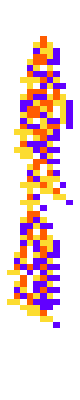
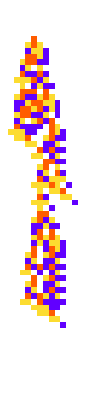
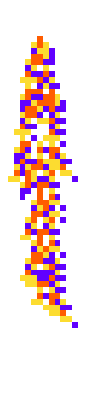
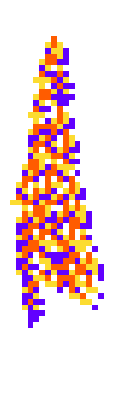
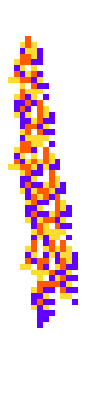
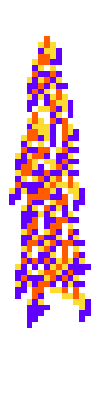
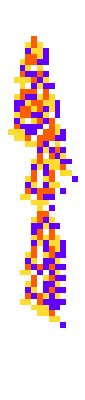
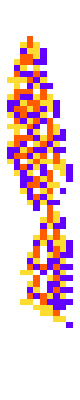
{-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50,-Graphics-50}

```mathematica
With[{ca = CellularAutomaton[#, {{1}, 0}, 55]}, Labeled[ArrayPlot[ca, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]],{{"[◼]", "TestCALifeTime"}}[ca]]]&/@
```

```mathematica
Table[Length[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == i&]], {i, 10, 50}]
```

{936,1091,887,856,716,683,583,535,398,352,333,317,279,249,188,173,149,149,101,119,130,113,81,78,61,60,70,60,68,66,47,57,47,38,47,35,39,36,21,28,47}

```mathematica
Table[Length[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == i&]], {i, 40, 60}]
```

{47,57,47,38,47,35,39,36,21,28,47,43,25,29,20,15,20,22,26,21,12}

```mathematica
Total[]
```

675

```mathematica
Length[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 11&]]
```

1091

```mathematica
RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 11&], 1]
```

<|{537074854188,32897023}→11|>

```mathematica
KeyVaWith[{ca = CellularAutomaton[#, {{1}, 0}, 55]}, ArrayPlot[ca, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]]&/@ RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 11&], 1]
```

$Aborted

```mathematica
SeedRandom[333333];GraphicsGrid[Partition[KeyValueMap[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, 15], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], # == 11&], 100]], 10]]
```

-Graphics-

```mathematica
SeedRandom[333333];GraphicsGrid[Partition[KeyValueMap[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, {65, {-15, 15}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,RandomSample[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], 40<=#<=60&], 105]], 15]]
```

-Graphics-

```mathematica
polys=Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-10,30}}},SeedRandom[6353];
ReverseSort@*Counts@*({{"[◼]", "CAPolygon"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,#,"ReturnPerturbations"->False]]&/@#&)@{{"[◼]", "allperts"}}[ru,init,txspec]];
```

```mathematica
Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={200,{-10,30}}},GraphicsRow[KeyValueMap[Labeled[Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63],AbsoluteDashing[{4,1}],AbsoluteThickness[1.25]}],Hue[0.73,0.14,0.93,0.36], ,#1},Frame->True,FrameTicks->None,FrameStyle->GrayLevel[0,.25],ImageSize->{Automatic,200},PlotRange->{{0,40},{80,201}}],Text[NumberForm[N[#2/Length[{{"[◼]", "allperts"}}[ru,init,txspec]],2]]]]&,(Take[#,UpTo@8])&@polys]]]
```

```mathematica
polys =ParallelMap[ {{"[◼]", "CAPolygon"}}[CellularAutomaton[{#[[1]], 3, 1},{{1}, 0}, {65, {-20, 20}}]]&, Keys[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], 40<=#<=60&]]];
```

```mathematica
sorted = SortBy[polys, Area];
```

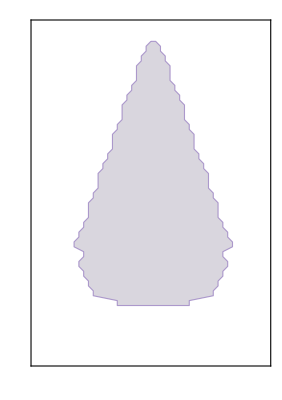
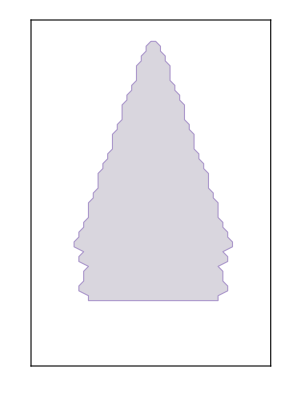
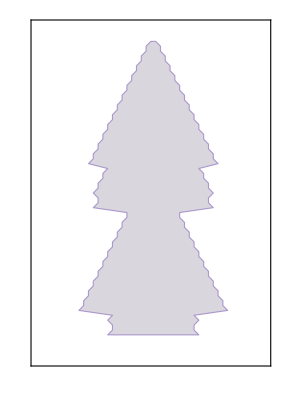
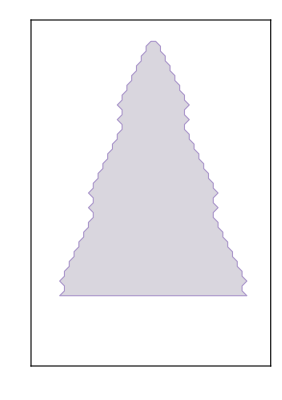
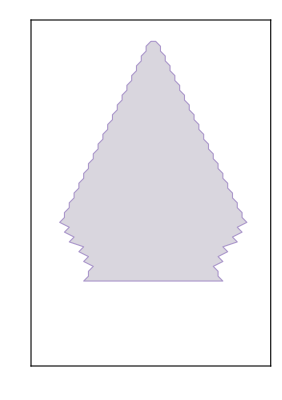
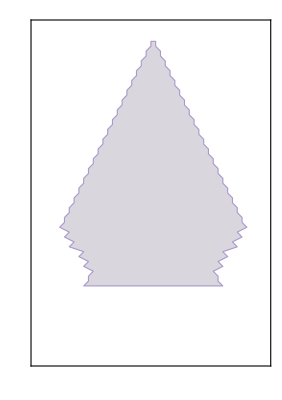
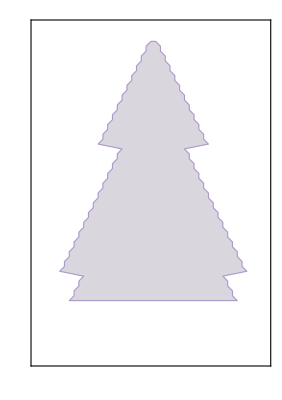
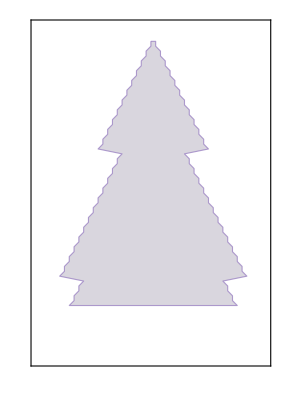
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}]&/@sorted[[-30;;]]
```

```mathematica
Length[polys]
```

675

```mathematica
Length[Union[polys]]
```

651

```mathematica
Length/@ Gather[polys]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}, ImageSize->50]&/@sorted[[-40;;]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}]&/@polys]
```

```mathematica
FeatureSpacePlot[Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}]&/@polys]
```

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},ArrayPlot[Map[Blend[Take[Last/@{{"[◼]", "CustomStyleData"}}["Colors"],4],BinCounts[#,{0,4,1}]]&,Transpose[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {150, {-10, 40}}, #, "ReturnPerturbations"->False]&/@ {{"[◼]", "allperts"}}[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}]],{3,1,2}],{2}]]]
```

```mathematica
aps  = KeyValueMap[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, {65, {-15, 15}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&,Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], 40<=#<=60&]];
```

```mathematica
Magnify[FeatureSpacePlot[Rasterize[#]->#&/@ aps, LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000], .31]
```

-Graphics-

```mathematica
((Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}, ImageSize->50]&)/@ polys)[[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Magnify[FeatureSpacePlot[Rasterize[#]->#&/@ 
((Graphics[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.36],.3],#},Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}]&)/@ polys)
, LabelingSize->100,PlotStyle->AbsolutePointSize[9],Frame->True,FrameTicks->None,FrameStyle->Gray,RandomSeeding->64453,PerformanceGoal->"Static",ImageSize->2000], .31]
```

-Graphics-

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},ArrayPlot[Map[Blend[Take[Last/@{{"[◼]", "CustomStyleData"}}["Colors"],4],BinCounts[#,{0,4,1}]]&,Transpose[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {150, {-10, 40}}, #, "ReturnPerturbations"->False]&/@ {{"[◼]", "allperts"}}[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}]],{3,1,2}],{2}]]]
```

```mathematica
Transpose[{{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {150, {-10, 40}}, #, "ReturnPerturbations"->False]&/@ {{"[◼]", "allperts"}}[CellularAutomaton[ru, {{1}, 0}, {150, {-10, 40}}]],{3,1,2}]
```

```mathematica
Transpose[CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, {65, {-15, 15}}]&/@ Keys[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], 40<=#<=60&]], {3, 1, 2}]
```

```mathematica
ArrayPlot[Map[Blend[Take[Last/@{{"[◼]", "CustomStyleData"}}["Colors"],4],BinCounts[#,{0,4,1}]]&,,{2}]]
```

-Graphics-

```mathematica
BarChart[{{1, 2, 3}}, ChartLayout->"Stacked", ChartStyle->{Red, Green ,Blue}]
```

-Graphics-

```mathematica
Map[BinCounts[#, {0, 3, 1}]&, , {2}]
```

```mathematica
Dimensions[]
```

{66,31,3}

```mathematica
Histogram3D[{{{1, 1}, {1, 1}}, {{1, 1}, {1, 1}}}, ChartLayout->"Stacked"]
```

-Graphics3D-

```mathematica
Histogram3D[RandomVariate[NormalDistribution[0,1],{500,2}]]
```

```mathematica
Position[Map[Blend[Take[Last/@{{"[◼]", "CustomStyleData"}}["Colors"],4],BinCounts[#,{0,4,1}]]&,,{2}], Except[White], Heads->False]
```

```mathematica
SparseArray[]
```

```mathematica
Position[#, 0]&/@
```

```mathematica
Histogram3D[Table[RandomVariate[NormalDistribution[0,1],{500,2}], 2], ChartLayout->"Stacked"]
```

-Graphics3D-

```mathematica
cas =CellularAutomaton[{#1[[1]], 3, 1},{{1}, 0}, {65, {-15, 15}}]&/@ Keys[Select[{{"[◼]", "$LifetimeData"}}[3, 1,"Symmetric"], 40<=#<=60&]];
```

```mathematica
idxs = Table[Position[#, i]&/@ cas, {i, 0,2}]
```

```mathematica
cidxs = Catenate/@idxs;
```

```mathematica
cidxs[[1]]
```

```mathematica
Most[{{"[◼]", "CustomStyleData"}}["Colors"]]
```

{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1]}

```mathematica
Length/@Catenate/@idxs
```

{1087151,142296,151603}

```mathematica
Histogram3D[Catenate/@idxs, ChartLayout->"Stacked", ChartStyle->Most[{{"[◼]", "CustomStyleData"}}["Colors"]]]
```

-Graphics3D-

```mathematica
ListPlot3D[]
```

```mathematica
(Graphics[Join[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@Darker[Hue[0.73,0.14,0.93,0.05],.3]}, polys],Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}])
```

-Graphics-

```mathematica
Darker[Hue[0.73,0.14,0.93,0.36],.3]
```

RGBColor[0.5944932, 0.55986, 0.651, 0.36]

```mathematica
InputForm@RGBColor[0.5944932, 0.55986, 0.651, 0.1]
```

RGBColor[0.5944932, 0.55986, 0.651, 0.1]

```mathematica
(Graphics[Join[{EdgeForm[Opacity[.3, GrayLevel[.6]]],FaceForm@Opacity[.05, GrayLevel[.9]]}, polys],Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}])
```

-Graphics-

```mathematica
(Graphics[Join[{EdgeForm[{Hue[0.73,0.43,0.72,0.63]}],FaceForm@None}, polys],Frame->True,FrameTicks->None,PlotRange->{{-3,45},{0,68}}])
```

-Graphics-